```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]]
```

```mathematica
(* Here are the different operators *)
```

```mathematica
operatorHadamard = QuantumMatrixOperation["Hadamard"];
```

```mathematica
operatorRotate = QuantumMatrixOperation[{"RotZ",Pi/4}];
```

```mathematica
operatorCNOT = QuantumMatrixOperation["CNOT"];
```

```mathematica
operatorPauliZ = QuantumMatrixOperation["SigmaZ"];
```

```mathematica
operatorPauliY = QuantumMatrixOperation["SigmaY"];
```

```mathematica
operatorSqrtNOT = QuantumMatrixOperation[1/2*{{1+I,1-I},{1-I,1+I}}];
```

```mathematica
operatorFourier = QuantumMatrixOperation[{"Fourier",2}];
```

```mathematica
(* states for test *)
```

```mathematica
states ={QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{0,1},{1,0}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}]};
```

```mathematica
(* fixing normalization *)
```

```mathematica
fixStupidity[expression_]:=((expression)//.{Sqrt[x_]->x,Power[x_,Rational[1,n_Integer]]->x,Power[x_,Rational[-1,n_Integer]]->1/x})
```

```mathematica
(* get state or control qubit *)
```

```mathematica
getState[cell_]:= QuantumPartialTr[cell,{2}]
```

```mathematica
getControlled[cell_]:=QuantumPartialTr[cell,{1}]
```

```mathematica
(* create entangled state and measurement *)
```

```mathematica
generateEntangledState[]:=QuantumFiniteDimensionalState[{"PhiPlus"}]
```

```mathematica
entangledpair = generateEntangledState[];
```

```mathematica
entangledMeasurement = QuantumMeasurement["Observable"-> "SigmaX"];
```

```mathematica
(* create QFDS, of state qubit (j+1) and entangled states *)
(* apply CNOT on state qubit and first entangled qubit *)
(* apply Hadamard on state qubit *)
(* measure state qubit and second entangled qubit *)
```

```mathematica
entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[getState[states[[j+1]]]["StateVector"]],Normal[pair["StateVector"]]}]]/;j≠Length[states]

entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[getState[states[[1]]]["StateVector"]],Normal[pair["StateVector"]]}]]/;j===Length[states]
```

```mathematica
chooseTeleportationOperation[pair_,states_,j_Integer]:=
Flatten[{QuantumEvaluate[{1}-> entangledMeasurement,
QuantumEvaluate[{1}-> operatorHadamard,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]],QuantumEvaluate[{2}-> entangledMeasurement,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]
}]
```

```mathematica
chooseTeleportationOperation[generateEntangledState[],states,1];
```

```mathematica
(*Apply chosen operation to control qubit, change operations to something more interesting, if that is fixed up*)
```

```mathematica
applyControlOperation[pair_,states_,j_Integer]:=
Module[{answer=chooseTeleportationOperation[pair,states,j]},
Which[
answer==={-1,-1},
QuantumEvaluate[{1}-> operatorHadamard,getControlled[states[[j]]]],
answer==={-1,1},
QuantumEvaluate[{1}-> operatorCNOT,getControlled[states[[j]]]],
answer==={1,-1},
QuantumEvaluate[{1}-> operatorCNOT,getControlled[states[[j]]]],
answer==={1,1},
QuantumEvaluate[{1}-> operatorHadamard,getControlled[states[[j]]]]]]
```

```mathematica
applyControlOperation[generateEntangledState[],states,1]
```

QuantumFiniteDimensionalState[…]

```mathematica
(* create new cell based on new control qubit, teleported state qubit, and both of them put through an operator *)
```

```mathematica
createNewCell[j_Integer,states_,pair_,operator1_]:= 
QuantumEvaluate[{1,2}-> operator1,QuantumFiniteDimensionalState[fixStupidity[
{Normal[applyControlOperation[pair,states,j]["StateVector"]],Normal[getState[states[[j]]]["StateVector"]]}]]]
```

```mathematica
createNewCell[1,states,generateEntangledState[], operatorFourier]
```

QuantumFiniteDimensionalState[…]

```mathematica
(* What Airty 2 operations do in terms of mixing things up so you can't separate individual qubits after, this was applying final operation of operatorCNOT followed by operatorFourier *)
```

```mathematica
Normal[QuantumFiniteDimensionalState[…]["StateVector"]]
```

{1/(√2),-1/2 (-1)^(3/4),0,1/2 (-1)^(1/4)}

```mathematica
QuantumPartialTr[QuantumFiniteDimensionalState[…],{1}]
```

Greater::nord: Invalid comparison with (1/8+ⅈ/8) ((1-ⅈ)-2 (-1)^(3/4)-(-1)^(3/4) √2) attempted.

Greater::nord: Invalid comparison with (1/8+ⅈ/8) ((1-ⅈ)+2 (-1)^(3/4)-(-1)^(3/4) √2) attempted.

CoordinateTransformData::notent: Cartesian→Spherical is not a known entity, class, or tag for CoordinateTransformData. Use CoordinateTransformData[] for a list of entities.

CoordinateTransformData::notent: Abs[Cartesian→Spherical] is not a known entity, class, or tag for CoordinateTransformData. Use CoordinateTransformData[] for a list of entities.

Set::shape: Lists {QuantumComputing`Private`r$224811,QuantumComputing`Private`θ$224811,QuantumComputing`Private`ϕ$224811} and CoordinateTransformData[Abs[Cartesian→Spherical],Abs[Mapping],{1/4,1/4,Abs[1/2-((1/4-ⅈ/4) (-1)^(1/4))/(√2)+((1/4+ⅈ/4) (-1)^(3/4))/(√2)]}] are not the same shape.

QuantumFiniteDimensionalState[…]

```mathematica
(* repeat for all *)
```

```mathematica
nextState[operator1_,pair_,states_]:= createNewCell[#,states,pair,operator1]&/@Range[Length[states]]
```

```mathematica
allStates[operator1_,pair_,states_,n_Integer]:= NestList[nextState[operator1,pair,#]&,states,n]
```

```mathematica
(* in CA, finding disorder and randomness from initial structure is a surprise, in QCA finding order is a surprise? *)
```

```mathematica
(*Visualization*)
```

```mathematica
separateStates[states_]:= Map[{Normal[getState[#]["StateVector"]],Normal[getControlled[#]["StateVector"]]}&,states]
separateAllStates[states_]:= separateStates[#]&/@states
```

```mathematica
separateAllStates[allStates[operatorFourier,generateEntangledState[],states,10]]
```

{{{{1,0},{0,1}},{{0,1},{1,0}},{{1,0},{0,1}}},{{{1/(√2),1/(√2)},{1,0}},{{1/(√2),-1/(√2)},{1,0}},{{1/(√2),1/(√2)},{1,0}}},{{{1,0},{1,0}},{{0,1},{1,0}},{{1,0},{1,0}}},{{{1/(√2),1/(√2)},{1,0}},{{1/(√2),-1/(√2)},{1,0}},{{1/(√2),1/(√2)},{1,0}}},{{{1,0},{1,0}},{{0,1},{1,0}},{{1,0},{1,0}}},{{{1/(√2),1/(√2)},{1,0}},{{1/(√2),-1/(√2)},{1,0}},{{1/(√2),1/(√2)},{1,0}}},{{{1,0},{1,0}},{{0,1},{1,0}},{{1,0},{1,0}}},{{{1/(√2),1/(√2)},{1,0}},{{1/(√2),-1/(√2)},{1,0}},{{1/(√2),1/(√2)},{1,0}}},{{{1,0},{1,0}},{{0,1},{1,0}},{{1,0},{1,0}}},{{{1/(√2),1/(√2)},{1,0}},{{1/(√2),-1/(√2)},{1,0}},{{1/(√2),1/(√2)},{1,0}}},{{{1,0},{1,0}},{{0,1},{1,0}},{{1,0},{1,0}}}}

```mathematica
getColour[com_]:= RGBColor[N[Re[com],10],0,N[Im[com],10]]/;Re[com]≥ 0&&Im[com]≥0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],RGBColor[0,0,N[Im[com],10]]}]/;Re[com]≤ 0&&Im[com]≥0
getColour[com_]:= Blend[{RGBColor[Abs[N[Re[com],10]],0,0],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≥ 0&&Im[com]≤0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≤ 0&&Im[com]≤0
```

```mathematica
colourQubit[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧]}
```

```mathematica
colourQubit[{1,0}];
```

```mathematica
colourQubit[{0,I}];
```

```mathematica
colourQubit[{-1,0}];
```

```mathematica
colourQubit[{0,-I}];
```

```mathematica
colourCell[cell_]:= {colourQubit[cell⟦1⟧],colourQubit[cell⟦2⟧]}
```

```mathematica
colourState[state_]:=Map[colourCell,state]
```

```mathematica
colourAll[allstates_]:=Map[colourState, allstates]
```

```mathematica
showQubit[qubit_]:= Rotate[ArrayPlot[{colourQubit[qubit]},Frame-> False,PlotRangePadding->None],3Pi/2]
```

```mathematica
showQubit[{1,0}];
```

```mathematica
showCell[cell_]:= Row[{showQubit[cell⟦1⟧],showQubit[cell⟦2⟧]}]
```

```mathematica
showCell[{{1,0},{0,1}}];
```

```mathematica
showState[state_]:=Map[showCell,state]
```

```mathematica
showAll[allState_]:= Grid[Map[showState,allState]]
```

```mathematica
QuantumCellularAutomata[operator1_,initialstate_,steps_Integer]:= showAll[separateAllStates[allStates[operatorFourier,generateEntangledState[],initialstate,steps]]]
```

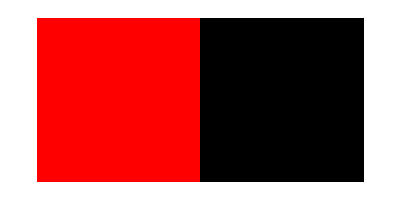
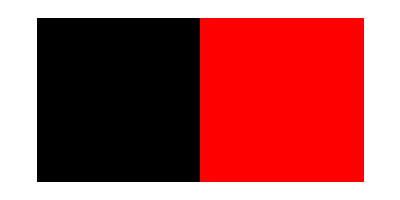
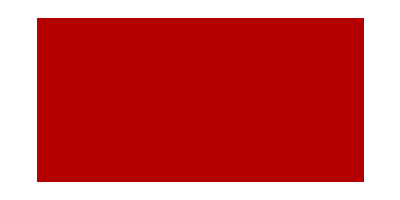
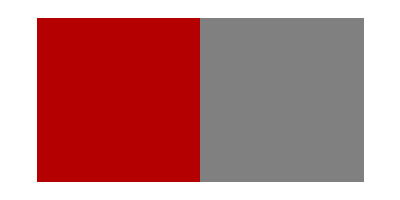
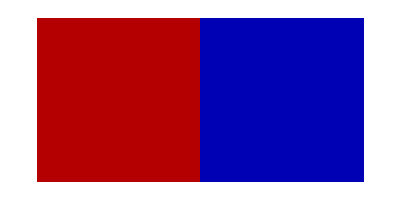
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
QuantumCellularAutomata[operatorFourier,{QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{1,0}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}],QuantumFiniteDimensionalState[{{1,0},{0,1}}]},10]
```